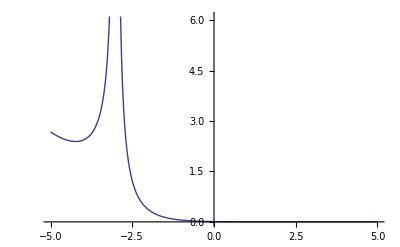

0.166667-0.025641 (-3.+x)+0.003663 (-3.5+x) (-3.+x)-0.0004884 (-4.+x) (-3.5+x) (-3.+x)+0.0000610501 (-4.5+x) (-4.+x) (-3.5+x) (-3.+x)-7.18236×10^-6 (-5.+x) (-4.5+x) (-4.+x) (-3.5+x) (-3.+x)+7.9804×10^-7 (-5.5+x) (-5.+x) (-4.5+x) (-4.+x) (-3.5+x) (-3.+x)

{0.166667,0.153846,0.142857,0.133333,0.125,0.117647,0.111111}

{0.166667,0.153846,0.142857,0.133333,0.125,0.117647,0.111111}

```mathematica
f[x_]:=1/(3+x);
k=6;
X={};
Do [X=Append[X, (3+0.5*i)], {i,0,k,1}];

(*
k=5;
f[x_]=E^(6x);
X={0,0,0,1,1};
*)

n=Length[X];
Y=f[X];
A=ConstantArray[0,{n,n}];
A[[All,1]]=Y; (*first column initialized*)
i=2;
While[i≤n,k=i;
While[k≤n,
If[X[[k]]-X[[k-i+1]]≠0,A[[k,i]]=(A[[k,i-1]]-A[[k-1,i-1]])/(X[[k]]-X[[k-i+1]]),A[[k,i]]=(A[f[x],{x,i-1}]/.x->X[[k]])/Factorial[i-1]];
k=k+1];
i=i+1];
pn[x_]=Sum[A[[i]][[i]]Product[x-X[[k]],{k,1,i-1}],{i,1,n}];
Plot[Abs[f[x]-pn[x]],{x,-5,5}]
pn[x]
pn[X]
f[X]
```